# gaussian n cutoff

## fix σ; calculate <g|ρ|g> for ε = 10Ω; plot as a function of power of k

## parameters

```mathematica
α=1;
Ω=1;
ε=10 Ω;
```

```mathematica
numSteps=7;
nMin=1;nMax=8; nStepSize=Abs[nMin-nMax]/numSteps;
nValues=Table[n,{n,nMin,nMax,nStepSize}];
```

```mathematica
nValues
```

{1,2,3,4,5,6,7,8}

## smearing function

```mathematica
σ0=10^-4/Ω;
σ=σ0;
σNorm=σ/σ0;
```

```mathematica
f[x_]:=1/(σ*√π)ⅇ^(-x^2/σ^2)
ftil[k_]:=FourierTransform[f[x],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

## switching function

```mathematica
chiT1[t_]:=1/(r+T)1/2*(1+Cos[π/r(t+T/2)])
chiT2[t_]:=1/(r+T)
chiT3[t_]:=1/(r+T)1/2*(1+Cos[π/r(t-T/2)])
```

## k integrand

### the first interval

```mathematica
tpInt1[t_?NumericQ,k_?NumericQ]:=tpInt1[t,k]=NIntegrate[chiT1[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T/2-r,t}]
```

```mathematica
tInt1[k_?NumericQ]:=tInt1[k]=α*NIntegrate[chiT1[t] tpInt1[t,k],
{t,-T/2-r,-T/2}]
```

### the second interval

```mathematica
tpInt2[t_,k_]:=Integrate[chiT2[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T/2,t}]
```

```mathematica
tInt2[k_]:=α*Integrate[chiT2[t] tpInt2[t,k],
{t,-T/2,T/2}]
```

### the third interval

```mathematica
tpInt3[t_?NumericQ,k_?NumericQ]:=tpInt3[t,k]=NIntegrate[chiT3[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,T/2,t}]
```

```mathematica
tInt3[k_?NumericQ]:=tInt3[k]=α*NIntegrate[chiT3[t] tpInt3[t,k],
{t,T/2,T/2+r}]
```

this integrand with the transition from Abs[k] → k taken into account (i.e. can now properly integrate from 0 to ∞ with proper factor of 2)

```mathematica
kIntegrand[k_]:=-1/π*k*ftil[k]^2*(tInt1[k]+tInt2[k]+tInt3[k])
```

## cutoff function

```mathematica
gaussNCutoff[k_,n_]:=ⅇ^((-Abs[k]^n)/(2 ε^n));
lorNCutoff[k_,n_]:=ε^n/(Abs[k]^n+ε^n);
```

## <g|ρ|g>

```mathematica
T=2;r=0.2;
```

```mathematica
pGaussN=Table[α+λ^2*NIntegrate[gaussNCutoff[k,n]*kIntegrand[k],{k,0,∞}],{n,nMin,nMax,nStepSize}]
```

{0.996267,0.996535,0.996621,0.99666,0.99668,0.996693,0.996701,0.996707}

```mathematica
pLorN=Table[α+λ^2*NIntegrate[lorNCutoff[k,n]*kIntegrand[k],{k,0,∞}],{n,nMin,nMax,nStepSize}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {4.81037×10^7}. NIntegrate obtained -0.364902 and 0.0000158614 for the integral and error estimates.

{0.996351,0.996543,0.996615,0.996657,0.996682,0.996697,0.996706,0.996713}

```mathematica
(*the following had improper values of T to have chi be normalized*)
```

```mathematica
pGaussN=Table[α+λ^2*NIntegrate[gaussNCutoff[k,n]*kIntegrand[k],{k,0,∞}],{n,nMin,nMax,nStepSize}]
```

{1-0.561903 λ^2,1-0.544127 λ^2,1-0.536398 λ^2,1-0.532657 λ^2,1-0.530611 λ^2,1-0.529371 λ^2,1-0.528556 λ^2,1-0.527988 λ^2,1-0.527572 λ^2,1-0.486719 λ^2}

```mathematica
pLorN=Table[α+λ^2*NIntegrate[lorNCutoff[k,n]*kIntegrand[k],{k,0,∞}],{n,nMin,nMax,nStepSize}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {4.81037×10^7}. NIntegrate obtained -0.544834 and 0.0000307297 for the integral and error estimates.

{1-0.544834 λ^2,1-0.54219 λ^2,1-0.536897 λ^2,1-0.532932 λ^2,1-0.530485 λ^2,1-0.528975 λ^2,1-0.528005 λ^2,1-0.527354 λ^2,1-0.526898 λ^2,1-0.526569 λ^2}

```mathematica
pGaussN[[10]]=α+λ^2*NIntegrate[gaussNCutoff[k,10]*kIntegrand[k],{k,0,∞},WorkingPrecision->100]
```

NIntegrate::precw: The precision of the argument function (-ⅇ^-k^2/200000000 - Abs[k]^10/20000000000\ k\ (Sin[2 - 2\ k]^2/(2.2  - 2.2\ k)^2 + Sin[2\ (1 + k)]^2/(« 1 »)^2 + tInt1[k] + tInt3[k])/π
) is less than WorkingPrecision (100.).

NIntegrate::levtime: Time spent solving linear system in LevinRule exceeded 10. seconds. Try increasing the value of the "TimeConstraint" option or decreasing the value of the "Points" option.

NIntegrate::mtdfb: Numerical integration with "LevinRule" failed. The integration continues with Method -> "GaussKronrodRule".

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {1.000001669999824250837580329924460783833713524577146756566646589252161051195868006517051652697487422}. NIntegrate obtained -0.5272578098402679242701816945620187921663707687752372968064244887594562460742144875584473077893099022 and 7.662647783247701096759406246312003589886856880830746452375917468435079047914142335390652916808793236×10^-14 for the integral and error estimates.

1-0.5272578098402679242701816945620187921663707687752372968064244887594562460742144875584473077893099022 λ^2

```mathematica
(*pGaussN[[10]]=0.9984726539327919*)
```

## plot

```mathematica
λ=0.1;Ω=.;
```

```mathematica
dataGaussN=Transpose[{nValues,pGaussN}];
dataLorN=Transpose[{nValues,pLorN}];
```

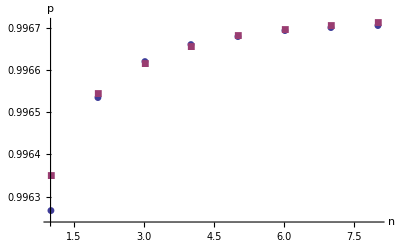

```mathematica
ListPlot[{dataGaussN,dataLorN},
AxesLabel->{n,p}, 
PlotMarkers->Automatic,
PlotLabel->Style["",FontSize->16]]
```

## save the data!!

```mathematica
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pGaussNvN.csv",dataGaussN];
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pLorNvN.csv",dataLorN];
```

```mathematica
dataGaussN
```

{{1,0.994381},{2,0.994559},{3,0.994636},{4,0.994673},{5,0.994694},{6,0.994706},{7,0.994714},{8,0.99472},{9,0.994724},{10,0.994727}}

## plot gaussian with lorentzian

```mathematica
(*dataLorN=Import["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pLorNvN.csv"];
dataGaussN=Import["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pGaussNvN.csv"];*)
```

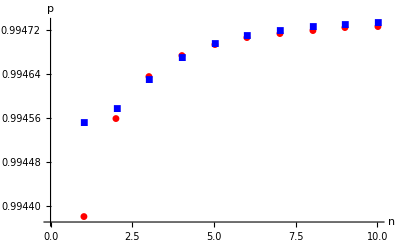

```mathematica
ListPlot[{dataGaussN,dataLorN},
AxesLabel->{n,p},
PlotStyle->{Red,Blue},
PlotMarkers->Automatic,
PlotLabel->Style["",FontSize->16]]
```

```mathematica
basePath="C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/";
```

```mathematica
dataSharp=Import[FileNameJoin[{basePath,"pSharpvEpsilon.csv"}]];
```

```mathematica
pLorN=dataLorN[[All,2]];
pGaussN=dataGaussN[[All,2]];
nValues=dataLorN[[All,1]];
```

```mathematica
pSharp=dataSharp[[6,2]];
```

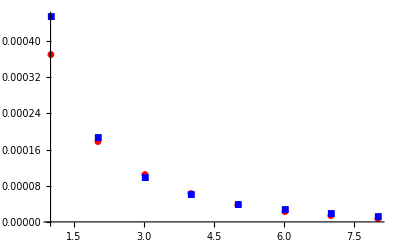

```mathematica
ListPlot[{Transpose[{nValues,Abs[pLorN-pSharp]/pLorN}],Transpose[{nValues,Abs[pGaussN-pSharp]/pGaussN}]},
PlotStyle->{Red,Blue},
PlotMarkers->Automatic]
```